### Set up the expression for displacement u(x)

```mathematica
ClearAll[P,Ε,EA,u]

P[X_,F_:0]:=Piecewise[{
{50000-F,X≤0.7},
{50000 ,1.0≥ X>0.7}
}
];
 (* in Newtons*)

A[X_]=Piecewise[{
{π(50/2  10^-3)^2,X≤0.7},
{π(30/2  10^-3)^2 ,1.0≥ X>0.7}
}
];
(*Area, meters^2*)

Ε[X_,E1_:200,E2_:200]:=Piecewise[{
{ E1 * 10^9,X≤0.7},
{ E2 *10^9,1.0≥ X>0.7}
}
];
(*Young's modulus, in Newtons/meters^2*)
(* "E1_:200" and "E2_:200" each assigns the default value of E1=200 and E2=200 *)

EA[X_,E1_:200,E2_:200]:=A[X]Ε[X,E1,E2];(*Axial rigidity, in Newtons*)

u[X_,E1_:200,E2_:200,F_:0]:=NIntegrate[P[Y,F]/EA[Y,E1,E2],{Y,0,X}]
```

### (a) Both bars are steel (HW2, Problem 3 (ii)), F=110kN

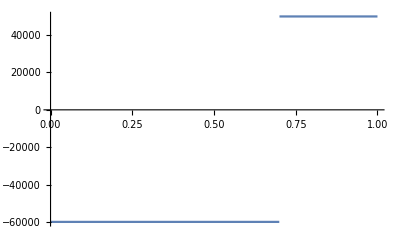

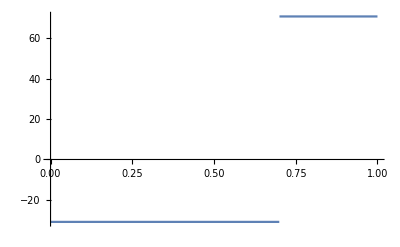

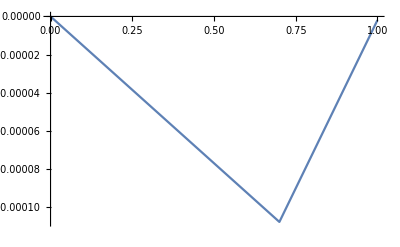

```mathematica
Plot[P[X,110 10^3],{X,0,1}] (*Axial force diagram*)
Plot[P[X,110.6 10^3]/(A[X]*10^6),{X,0,1}] (*Axial normal traction diagram (in MPa)*)
Plot[u[x,200,200,110.6 10^3],{x,0,1}] (*Displacement diagram*)
```

### (b) Top bar is made of steel, bottom bar is made of titanium alloy (HW2, Problem 3 (iii)), F=86.3kN

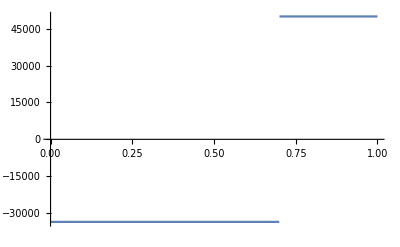

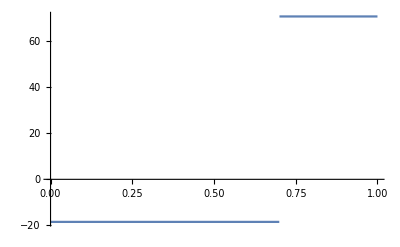

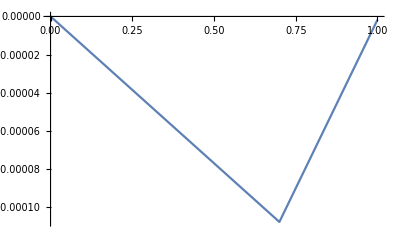

```mathematica
Plot[P[X,83.6 10^3],{X,0,1}](*Axial force diagram*)

Plot[P[X,86.3 10^3]/(A[X]*10^6),{X,0,1}](*Axial normal traction diagram (in MPa)*)

Plot[u[x,120,200,86.3 10^3],{x,0,1}] (*Displacement diagram*)
```